## This shows that there is definitely an optimal way to reconstruct a function. In particular, we should use Reconstruct over Reconstruct2 and plot it in the way that generates times5.

### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]]
test[x_]:=Sin[Pi x]^2
dtest[x_]:=2 Pi Cos[Pi x] Sin[Pi x]
```

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
fullCoefficients[f_,l_]:={{f[1],f[0]}}~Append~Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]
Reconstruct2[coefficients_]:=coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[Sum[coefficients[[2,l,i]] ϕ[2^l(#-2^-l(2i-1))],{i,1,Length[coefficients[[2,l]]]}],{l,1,Length[coefficients[[2]]]}]&
Reconstruct[coefficients_]:=coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[coefficients[[2,l,Ceiling[2^(l-1)#]]] ϕ[2^l(#-2^-l(2Ceiling[2^(l-1)#]-1))],{l,1,Length[coefficients[[2]]]}]&
```

### Plot Times

```mathematica
times1=Table[Timing[Plot[Reconstruct[fullCoefficients[test,n]][x],{x,0,1}]][[1]],{n,1,8}]
times2=Table[Timing[Plot[Reconstruct2[fullCoefficients[test,n]][x],{x,0,1}]][[1]],{n,1,8}]
times3=Table[Timing[Plot[Reconstruct[fullCoefficients[test,n],x],{x,0,1}]][[1]],{n,1,8}]
times4=Table[Timing[Plot[(Reconstruct[#,x]),{x,0,1}]&[fullCoefficients[test,n]]][[1]],{n,1,8}]
times5=Table[Timing[Plot[(#[x]),{x,0,1}]&[Reconstruct[fullCoefficients[test,8]]]][[1]],{n,1,8}]
```

{0.016209,0.018683,0.058122,0.169919,0.390902,0.871127,1.79354,3.34127}

{0.015485,0.017155,0.066626,0.201403,0.483463,1.04095,2.19527,3.97823}

{0.008762,0.010031,0.014977,0.028602,0.049305,0.107974,0.220518,0.468607}

{0.008839,0.008315,0.008445,0.010605,0.014672,0.025897,0.0402,0.07597}

{0.119398,0.114179,0.116035,0.117829,0.11157,0.113414,0.115699,0.112885}

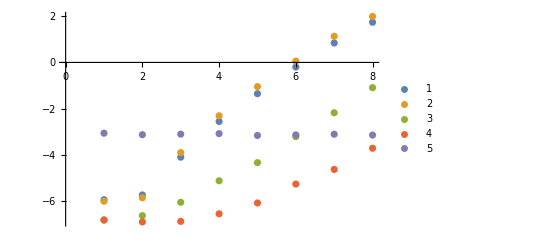

```mathematica
ListPlot[{times1,times2,times3,times4,times5}//Log2,PlotLegends->Automatic]
```